### Matex y Colores “Scientific”

```mathematica
<<MaTeX`
ClearAll[plotColors];
plotColors::usage="plotColors[plotType,plotTheme] gives a list of the colors used in a plot when several curves are drawn. Here plotType is, for example, Plot or ListLogPlot while plotTheme may be \"Scientific\", \"Classic\" etc.";
plotColors[plotType_,plotTheme_]:=("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme[plotTheme,plotType]))/.Directive[x_,__]:>x;
pltcolors=plotColors[ListLinePlot,"Scientific"];

flogticks[y1_,y2_]:=Module[{table1,table2},
table1={};
Do[
	Do[
		AppendTo[table1,{i*10^j,""}];
		,{i,1,9,1}]
		,{j,y1,y2}];
		table2=Table[{10^j,ToString[10]^ToString[j]},{j,y1,y2}];
	Do[
		If[table2[[k,1]]==1,table2=ReplacePart[table2,{k,2}->1]],
		{k,1,Length@table2}];
	Join[table1,table2]
];
fplotlabel[i_]:=Module[{},
Switch[i,
	1, "electron neutrino",
	2, "muon neutrino",
	3, "tau neutrino"
	]
];

mainconfig="/home/sane/mainhnlchain/mainconfig/";
hnlchain="/home/sane/mainhnlchain/hnlchain/";
hnldata="/home/sane/mainhnlchain/data/";
```

### Escalado

```mathematica
(* MAIN *)
d431pPOT=1.2*10^-6;
POTpyear=1.47*10^21;
ncm2=700*300;
ncm2=1;

(* BG *)
bgtotald431=20*10*10^6;
bgd431factor=1/bgtotald431*d431pPOT*POTpyear*1/ncm2
(* HNL MESON *)
totald431=10*10*10^6;
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
```

8.82×10^6

1.764×10^7

# bg-meta plot

```mathematica
fbgimport[idGun_]:=Module[{idGuns,xmin,xmax,nbins,xrange,nudata,nubardata,nutable,nubartable,name,namebar},
Switch[idGun,
	431, idGuns="431",
	-431, idGuns="431bar",
	411, idGuns="411",
	-411, idGuns="411bar",
	421, idGuns="421",
	-421, idGuns="421bar",
	_, Print["Invalid idGun: "<>ToString[idGun]];Return[]];
xmin=0;
xmax=40;
nbins=40;
xrange=N[Table[xmin+i*(xmax)/nbins,{i,0,nbins}]];
name=hnlchain<>"/bg/analysis-bg/"<>idGuns<>"-meta.dat";
namebar=hnlchain<>"/bg/analysis-bg/"<>idGuns<>"-metabar.dat";
If[FileExistsQ[name]&&FileExistsQ[namebar],
	nudata=Import[name];
	nubardata=Import[namebar];
	nutable={};
	nubartable={};
	Do[
	AppendTo[nutable,Table[{xrange[[l]],nudata[[i,l]]*bgd431factor},{l,1,nbins+1}]];
	AppendTo[nubartable,Table[{xrange[[l]],nubardata[[i,l]]*bgd431factor},{l,1,nbins+1}]];
	,{i,1,3}];
	AppendTo[bgnutable,nutable];
	AppendTo[bgnutablebar,nubartable];	
	,
	Print[name<>" NOT FOUND"];
	Print[namebar<>" NOT FOUND"];
	];
];
(* LLAMAR LA DATA-TABLE *)
fbg[idGun_,flavour_]:=Module[{},
	Switch[idGun,
		431, bgnutable[[1,flavour]],
		-431, bgnutable[[2,flavour]],
		411, bgnutable[[3,flavour]],
		-411, bgnutable[[4,flavour]],
		421, bgnutable[[5,flavour]],
		-421, bgnutable[[6,flavour]]
	]
];
fbgbar[idGun_,flavour_]:=Module[{},
	Switch[idGun,
		431, bgnutablebar[[1,flavour]],
		-431, bgnutablebar[[2,flavour]],
		411, bgnutablebar[[3,flavour]],
		-411, bgnutablebar[[4,flavour]],
		421, bgnutablebar[[5,flavour]],
		-421, bgnutablebar[[6,flavour]]
	]
];
(* IMPORTAR DATA *)
bgnutable={};
bgnutablebar={};
Do[
	fbgimport[idGun]
,{idGun,{431,-431}}];
```

/home/sane/mainhnlchain/hnlchain//bg/analysis-bg/431bar-meta.dat NOT FOUND

/home/sane/mainhnlchain/hnlchain//bg/analysis-bg/431bar-metabar.dat NOT FOUND

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["\\text{off-axis (m)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
ylabel2=MaTeX["\\nu/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
```

### Config Plots

```mathematica
framelabel={xlabel,ylabel2};
legends={latexnue,latexnumu,latexnutau,latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",2},LegendMarkerSize->16
],{0.85,0.82}];
frametickstyle=Directive[Black];
plotstyle={{pltcolors[[1]],Automatic},{pltcolors[[2]],Automatic},{pltcolors[[3]],Automatic},{pltcolors[[1]],Dashed},
{pltcolors[[2]],Dashed},{pltcolors[[3]],Dashed}};
plotstyle={{Lighter[Red,0.2],Automatic},{Lighter[Blue,0.2],Automatic},{Darker[Green,0.4],Automatic},{Lighter[Red,0.2],Dashed},{Blue,Dashed},{Darker[Green,0.4],Dashed}};
imagesize={300,Automatic};
plotrange={{0,40},{5*10^10,1*10^14}};
background=White;
yticks=Join[Table[{i*10^10,""},{i,1,9,1}],Table[{i*10^11,""},{i,1,9,1}],Table[{i*10^12,""},{i,1,9,1}],Table[{i*10^13,""},{i,1,9,1}],{{10^10,"10^10"},{10^11,"10^11"},{10^12,"10^12"},{10^13,"10^13"},{10^14,"10^14"}}];
xticks=Automatic;
frameticks={{yticks,Automatic},{xticks,None}};
```

### Plots

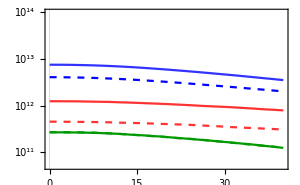

/home/sane/mainhnlchain/plots/bg-meta.pdf

```mathematica
bgplotexp=ListPlot[{fbg[431,1],fbg[431,2],fbg[431,3],fbgbar[431,1],fbgbar[431,2],fbgbar[431,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background]
Export[NotebookDirectory[]<>"bg-meta.pdf",bgplotexp]
```

# HNL meson

### Main Parameters

```mathematica
fmesonimport[idGun_]:=Module[{idGuns,xmin,xmax,nbins,xrange,name,namebar,nudata,nubardata,nutable,nutablebar},
Switch[idGun,
	431, idGuns="431",
	-431, idGuns="431bar",
	411, idGuns="411",
	-411, idGuns="411bar",
	421, idGuns="421",
	-421, idGuns="421bar",
	_, Print["Invalid idGun: "<>ToString[idGun]];Return[]];
xmin=0;
xmax=40;
nbins=40;
xrange=N[Table[xmin+i*(xmax-xmin)/nbins,{i,0,nbins}]];
name=hnlchain<>"dirac/meson/analysis/"<>idGuns<>"-meta.dat";
namebar=hnlchain<>"dirac/meson/analysis/"<>idGuns<>"-metabar.dat";
If[FileExistsQ[name]&&FileExistsQ[namebar],
	nudata=Import[name];
	nubardata=Import[namebar];
	nutable={};
	nutablebar={};
	Do[
		AppendTo[nutable,Table[{xrange[[l]],nudata[[i,l]]*d431factor},{l,1,nbins+1}]];
		AppendTo[nutablebar,Table[{xrange[[l]],nubardata[[i,l]]*d431factor},{l,1,nbins+1}]];
	,{i,1,15*3}];
	AppendTo[mesonnutable,nutable];
	AppendTo[mesonnutablebar,nutablebar];
	,
	Print[name<>" NOT FOUND"];
	Print[namebar<>" NOT FOUND"];
	];
]
(* LLAMAR LA DATA-TABLE *)
fmeson[idGun_,mhnl_,flavour_]:=Module[{},
	Switch[idGun,
		431, mesonnutable[[1,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-431, mesonnutable[[2,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		411, mesonnutable[[3,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-411, mesonnutable[[4,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		421, mesonnutable[[5,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-421, mesonnutable[[6,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]]
	]
];
fmesonbar[idGun_,mhnl_,flavour_]:=Module[{},
	Switch[idGun,
		431, mesonnutablebar[[1,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-431, mesonnutablebar[[2,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		411, mesonnutablebar[[3,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-411, mesonnutablebar[[4,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		421, mesonnutablebar[[5,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-421, mesonnutablebar[[6,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]]
	]
];
mesonnutable={};
mesonnutablebar={};
Do[
	fmesonimport[idGun]
,{idGun,{431}}];
```

### Data

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["\\text{off-axis (m)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
latext1=MaTeX["\\text{mHNL=1.9 GeV}",Magnification->magnificationlegends,ContentPadding->False];
```

### Config Plots

```mathematica
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle={{pltcolors[[1]],Automatic},{pltcolors[[2]],Automatic},{pltcolors[[3]],Automatic},{pltcolors[[1]],Dashed},{pltcolors[[2]],Dashed},{pltcolors[[3]],Dashed}};
imagesize={300,Automatic};
background=White;
yticks=flogticks[0,5];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
```

### Plots Nu

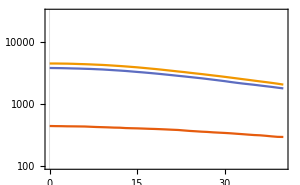

```mathematica
m=1.9;
plotrange={{0,40},{1*10^2,3*10^4}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{fmeson[431,m,1],fmeson[431,m,2],fmeson[431,m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>idGunString<>"-meta-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

### Plots Nubar

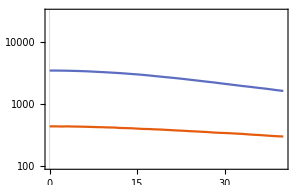

```mathematica
m=1.9;
plotrange={{0,40},{1*10^2,3*10^4}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{fmesonbar[431,m,1],fmesonbar[431,m,2],fmesonbar[431,m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexpbar=Show[plot1,text]
Export[NotebookDirectory[]<>idGunString<>"-metabar-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

# HNL tau

### Main Parameters

```mathematica
(* HNL MESON *)
totald431=8*10*10^6;
d431factor=1/totald431*d431pPOT*POTpyear*1/ncm2
(* FUNCION TAU IMPORT *)
ftauimport[idGun_]:=Module[{idGuns,xmin,xmax,nbins,xrange,name,namebar,nudata,nubardata,nutable,nutablebar},
Switch[idGun,
	431, idGuns="431",
	-431, idGuns="431bar",
	411, idGuns="411",
	-411, idGuns="411bar",
	421, idGuns="421",
	-421, idGuns="421bar",
	_, Print["Invalid idGun: "<>ToString[idGun]];Return[]];
xmin=0;
xmax=40;
nbins=40;
xrange=N[Table[xmin+i*(xmax-xmin)/nbins,{i,0,nbins}]];
name=hnlchain<>"dirac/tau/analysis/"<>idGuns<>"-meta.dat";
namebar=hnlchain<>"dirac/tau/analysis/"<>idGuns<>"-metabar.dat";
If[FileExistsQ[name]&&FileExistsQ[namebar],
	nudata=Import[name];
	nubardata=Import[namebar];
	nutable={};
	nutablebar={};
	Do[
		AppendTo[nutable,Table[{xrange[[l]],nudata[[i,l]]*d431factor},{l,1,nbins+1}]];
		AppendTo[nutablebar,Table[{xrange[[l]],nubardata[[i,l]]*d431factor},{l,1,nbins+1}]];
	,{i,1,15*3}];
	AppendTo[taunutable,nutable];
	AppendTo[taunutablebar,nutablebar];
	,
	Print[name<>" NOT FOUND"];
	Print[namebar<>" NOT FOUND"];
	];
]
(* LLAMAR LA DATA-TABLE *)
ftau[idGun_,mhnl_,flavour_]:=Module[{},
	Switch[idGun,
		431, taunutable[[1,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-431, taunutable[[2,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		411, taunutable[[3,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-411, taunutable[[4,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		421, taunutable[[5,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-421, taunutable[[6,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]]
	]
];
ftaubar[idGun_,mhnl_,flavour_]:=Module[{},
	Switch[idGun,
		431, taunutablebar[[1,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-431, taunutablebar[[2,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		411, taunutablebar[[3,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-411, taunutablebar[[4,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		421, taunutablebar[[5,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]],
		-421, taunutablebar[[6,IntegerPart[3*(mhnl-0.5)/0.1+flavour+0.001]]]
	]
];
taunutable={};
taunutablebar={};
Do[
	ftauimport[idGun]
,{idGun,{431}}];
```

### Data

### MaTeX

```mathematica
magnificationaxes=1.;
magnificationlegends=1.;
latexnue=MaTeX["\\nu_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumu=MaTeX["\\nu_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutau=MaTeX["\\nu_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
latexnuebar=MaTeX["\\bar{\\nu}_e",Magnification->magnificationlegends,ContentPadding->False];
latexnumubar=MaTeX["\\bar{\\nu}_{\\mu}",Magnification->magnificationlegends,ContentPadding->False];
latexnutaubar=MaTeX["\\bar{\\nu}_{\\tau}",Magnification->magnificationlegends,ContentPadding->False];
xlabel=MaTeX["\\text{off-axis (m)}",Magnification->magnificationaxes,ContentPadding->False];
ylabel=MaTeX["\\nu/\\text{cm}^{2}/\\text{yr}",Magnification->magnificationaxes,ContentPadding->False];
latext1=MaTeX["\\text{mHNL=1.9 GeV}",Magnification->magnificationlegends,ContentPadding->False];
```

### Config Plots

```mathematica
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle={{pltcolors[[1]],Automatic},{pltcolors[[2]],Automatic},{pltcolors[[3]],Automatic},{pltcolors[[1]],Dashed},{pltcolors[[2]],Dashed},{pltcolors[[3]],Dashed}};
imagesize={300,Automatic};
background=White;
yticks=flogticks[0,5];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
```

### Plots Nu

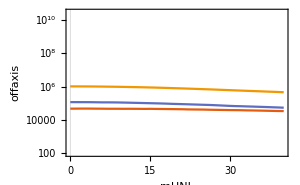

```mathematica
m=0.5;
plotrange={{0,40},{1*10^2,3*10^10}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{ftau[431,m,1],ftau[431,m,2],ftau[431,m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexp=Show[plot1,text]
Export[NotebookDirectory[]<>idGunString<>"-meta-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

### Plots Nubar

```mathematica
m=1.9;
plotrange={{0,40},{1*10^2,3*10^4}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnuebar,latexnumubar,latexnutaubar};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{ftaubar[431,m,1],ftaubar[431,m,2],ftaubar[431,m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexpbar=Show[plot1,text]
Export[NotebookDirectory[]<>idGunString<>"-metabar-"<>ToString[NumberForm[m,{2,1}]]<>".pdf",plotexp];
```

-Graphics-

# Meson + Tau

```mathematica
f431[mhnl_,flavour_]:=Module[{aux1,aux2,aux},
	aux1=fmeson[431,mhnl,flavour];
	If[Length@taunutable==1,
		aux2=ftau[431,mhnl,flavour];
		aux=Table[{aux1[[i,1]],aux1[[i,2]]+aux1[[i,2]]},{i,1,Length@aux1}],
		aux=aux1
	]
];
f431bar[mhnl_,flavour_]:=Module[{aux1,aux2,aux},
	aux1=fmesonbar[431,mhnl,flavour];
	If[Length@taunutable==1,
		aux2=ftaubar[431,mhnl,flavour];
		aux=Table[{aux1[[i,1]],aux1[[i,2]]+aux1[[i,2]]},{i,1,Length@aux1}],
		aux=aux1
	]
];
```

```mathematica
framelabel={xlabel,ylabel};
frametickstyle=Directive[Black];
plotstyle={{Lighter[Red,0.1],Automatic},{Lighter[Blue,0.1],Automatic},{Darker[Green,0.5],Automatic},{Lighter[Red,0.1],Dashed},{Lighter[Blue,0.1],Dashed},{Darker[Green,0.5],Dashed}};
imagesize={300,Automatic};
background=White;
yticks=flogticks[4,14];
xticks=Automatic;
frameticks={{yticks,None},{xticks,None}};
```

### Plots Nu

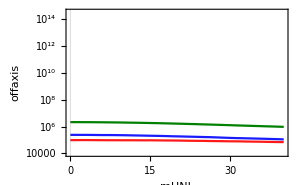

```mathematica
m=0.5;
plotrange={{0,40},{1*10^4,3*10^14}};
latext1=MaTeX["\\text{mHNL="<>ToString[NumberForm[m,{2,1}]]<>" GeV}",Magnification->magnificationlegends,ContentPadding->False];
text=Graphics[Text[latext1,Scaled[{0.2,0.925}]]];
legends={latexnue,latexnumu,latexnutau};
plotlegends=Placed[LineLegend[Automatic,legends,Spacings->0.01,LegendLayout->{"Column",1},LegendMarkerSize->16
],{0.9,0.825}];
plot1=ListPlot[{f431[m,1],f431[m,2],f431[m,3]},PlotTheme->"Scientific",FrameTicks->frameticks,FrameTicksStyle->frametickstyle,ScalingFunctions->{None,"Log"},PlotStyle->plotstyle,Joined->True,PlotLegends->plotlegends,ImageSize->imagesize,PlotRange->plotrange,FrameLabel->framelabel,Background->background];
plotexp=Show[plot1,text]
```

# Plots 3D

```mathematica
data431={};
Do[
	auxdata={};
	Do[
		AppendTo[auxdata,{mhnl,offaxis,f431[mhnl,i][[offaxis+1,2]]}]
	,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
	AppendTo[data431,auxdata];
,{i,1,3}];
data431bar={};
Do[
	auxdata={};
	Do[
		AppendTo[auxdata,{mhnl,offaxis,f431bar[mhnl,i][[offaxis+1,2]]}]
	,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
	AppendTo[data431bar,auxdata];
,{i,1,3}];
```

## Nu

### Density

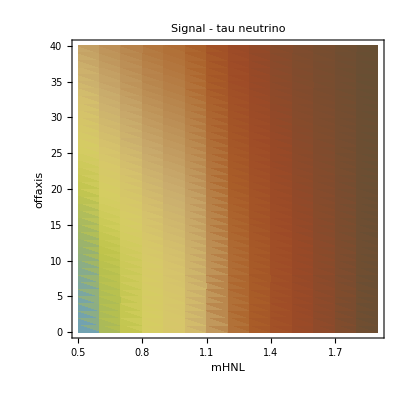

```mathematica
j=3;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks={Table[{i,AccountingForm[i]},{i,0,100000,5000}],Table[{i,AccountingForm[i]},{i,0,400000,10000}],Table[{i,AccountingForm[i]},{i,0,2000000,100000}]};
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[data431[[j]],PlotLegends->BarLegend[Automatic,Ticks->barlegendticks[[j]]],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal - "<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal-tau.png",plotexp,ImageResolution->300];
```

### 3D

```mathematica
j=3;
barlegendticks={Table[{i,AccountingForm[i]},{i,0,100000,10000}],Table[{i,AccountingForm[i]},{i,0,400000,50000}],Table[{i,AccountingForm[i]},{i,0,2000000,200000}]};
xticks=Table[mhnl,{mhnl,0.5,1.9,0.2}];
yticks=Table[offaxis,{offaxis,0,40,5}];
zticks=barlegendticks;
ticks={xticks,yticks,zticks[[j]]};
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListPlot3D[{data431[[j]]},ColorFunction->"SouthwestColors",BoxRatios->{2,2, 1.5},PlotLegends->BarLegend[Automatic,Ticks->barlegendticks[[j]]],InterpolationOrder->2,Ticks->ticks,AxesLabel->{xlabel,ylabel},PlotLabel->"Signal - "<>fplotlabel[j]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"signal3D-tau.png",plotexp,ImageResolution->300];
```

## NuBar

### Density

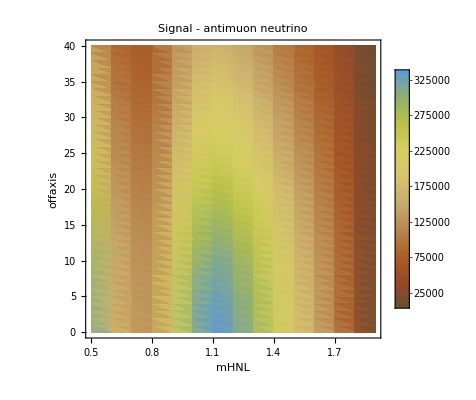

```mathematica
j=2;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks={Table[{i,i},{i,0,100000,2500}],Table[{i,i},{i,0,400000,25000}],Table[{i,i},{i,0,2000000,100000}]};
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[data431bar[[j]],PlotLegends->BarLegend[Automatic,Ticks->barlegendticks[[j]]],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal - anti"<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal-taubar.png",plotexp,ImageResolution->300];
```

### 3D

```mathematica
j=3;
barlegendticks={Table[{i,i},{i,0,100000,2500}],Table[{i,i},{i,0,400000,25000}],Table[{i,i},{i,0,2000000,100000}]};
xticks=Table[mhnl,{mhnl,0.5,1.9,0.2}];
yticks=Table[offaxis,{offaxis,0,40,5}];
zticks=barlegendticks;
ticks={xticks,yticks,zticks[[j]]};
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListPlot3D[{data431bar[[j]]},ColorFunction->"SouthwestColors",BoxRatios->{2,2, 1.5},PlotLegends->BarLegend[Automatic,Ticks->barlegendticks[[j]]],InterpolationOrder->2,Ticks->ticks,AxesLabel->{xlabel,ylabel},PlotLabel->"Signal - anti"<>fplotlabel[j]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"signal3D-taubar.png",plotexp,ImageResolution->300];
```

# BG vs Signal

## Nu

### Signal over BG

```mathematica
signalOverBg431={};
Do[
auxdata={};
Do[
AppendTo[auxdata,{mhnl,offaxis,f431[mhnl,i][[offaxis+1,2]]/fbg[431,i][[offaxis+1,2]]}]
,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
AppendTo[signalOverBg431,auxdata];
,{i,1,3}]
```

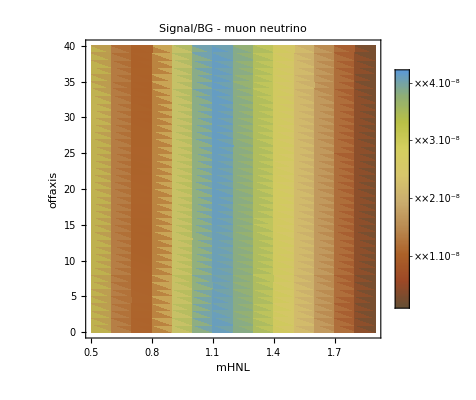

```mathematica
j=2;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks=Table[{i,ScientificForm[i,100]},{i,0,5000000,100000}];
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[signalOverBg431[[j]],PlotLegends->BarLegend[Automatic,Ticks->Automatic],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal/BG - "<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal2Bg-tau.png",plotexp,ImageResolution->300];
```

### Statistical Significance

```mathematica
signalOverSqrtBg431={};
Do[
auxdata={};
Do[
AppendTo[auxdata,{mhnl,offaxis,f431[mhnl,i][[offaxis+1,2]]/√(fbg[431,i][[offaxis+1,2]])}]
,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
AppendTo[signalOverSqrtBg431,auxdata];
,{i,1,3}]
```

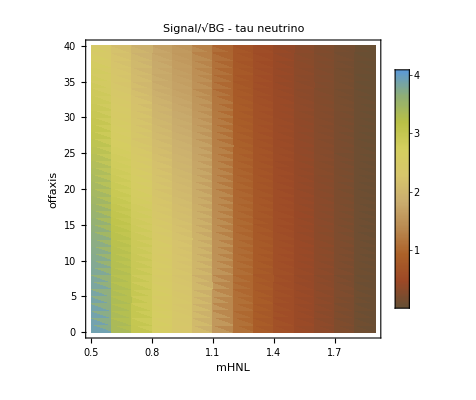

```mathematica
j=3;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks=Table[{i,ScientificForm[i,100]},{i,0,5000000,100000}];
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[signalOverSqrtBg431[[j]],PlotLegends->BarLegend[Automatic,Ticks->Automatic],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal/√BG - "<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal2sqrtBg-tau.png",plotexp,ImageResolution->300];
```

## NuBar

### Signal over BG

```mathematica
signalOverBg431bar={};
Do[
auxdata={};
Do[
AppendTo[auxdata,{mhnl,offaxis,f431bar[mhnl,i][[offaxis+1,2]]/fbgbar[431,i][[offaxis+1,2]]}]
,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
AppendTo[signalOverBg431bar,auxdata];
,{i,1,3}]
```

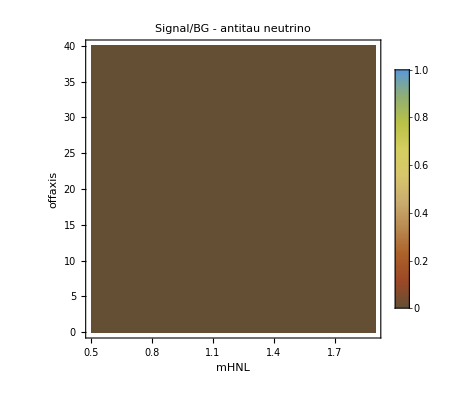

```mathematica
j=3;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks=Table[{i,ScientificForm[i,100]},{i,0,5000000,100000}];
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[signalOverBg431bar[[j]],PlotLegends->BarLegend[Automatic,Ticks->Automatic],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal/BG - anti"<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal2Bg-taubar.png",plotexp,ImageResolution->300];
```

### Statistical Significance

```mathematica
signalOverSqrtBg431bar={};
Do[
auxdata={};
Do[
AppendTo[auxdata,{mhnl,offaxis,f431bar[mhnl,i][[offaxis+1,2]]/√(fbgbar[431,i][[offaxis+1,2]])}]
,{mhnl,0.5,1.9,0.1},{offaxis,0,40,1}];
AppendTo[signalOverSqrtBg431bar,auxdata];
,{i,1,3}]
```

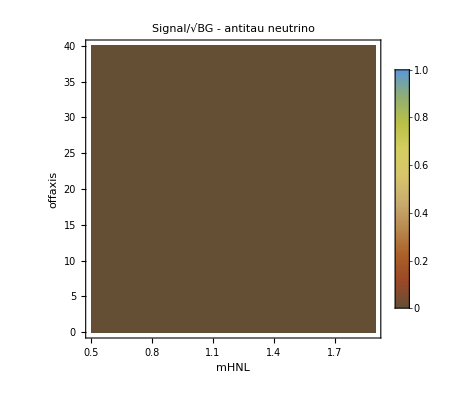

```mathematica
j=3;
xticks=Table[mhnl,{mhnl,0.5,1.9,0.1}];
yticks=Table[offaxis,{offaxis,0,40,5}];
frameticks={{yticks,Automatic},{xticks,Automatic}};
barlegendticks=Table[{i,ScientificForm[i,100]},{i,0,5000000,100000}];
xlabel="mHNL";
ylabel="offaxis";
plotexp=ListDensityPlot[signalOverSqrtBg431bar[[j]],PlotLegends->BarLegend[Automatic,Ticks->Automatic],InterpolationOrder->2,FrameTicks->frameticks,ColorFunction->"SouthwestColors",FrameLabel->{xlabel,ylabel},PlotLabel->"Signal/√BG - anti"<>fplotlabel[j]]
```

```mathematica
Export[NotebookDirectory[]<>"signal2sqrtBg-taubar.png",plotexp,ImageResolution->300];
```